Thomas Kwok
Math 385

# Homework 1

Create a title heading to include all problems in the homework exercise. 
Create section headings for each problem.

## Problem 1

Write an algorithm and implement a Mathematica code that generates
all odd integers from 1 to n.

Algorithm:
For i=1 to i=n, if i is odd then print i, else do not print.

```mathematica
n = 25;
For [loop =  1, loop ≤ n, loop++,
If [Mod[loop, 2] == 1, Print[loop], n-1]]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

## Problem 2

Write an algorithm and implement a Mathematica code that computes
the sum of the integers from 1 up to and including n.

Algorithm: 
Let p = 0. For i=1 to i=n, while i less than or equal to n, add i to p.

```mathematica
n = 100;
p= 0;
loop = 1;
While[loop≤ n, If[loop≤ n, p = p+loop]; loop++]
Print[p]
```

5050

## Problem 3

y(t) = Vo(t) - 1/2 gt^2
Vo = 10
g = 9.8

a. For any integer n, create n+1 uniformly spaced t values throughout interval [0, 2Vo/g]

```mathematica
Vo = 10;
g = 9.8;
n = 20;
interval = Table[{t*(2Vo/g)/n}, {t, 0, n}] ;
header = PrependTo[interval, {"t-value"}];
Grid[header]
```

t-value
0.
0.102041
0.204082
0.306122
0.408163
0.510204
0.612245
0.714286
0.816327
0.918367
1.02041
1.12245
1.22449
1.32653
1.42857
1.53061
1.63265
1.73469
1.83673
1.93878
2.04082

b. Create a function y(t)

```mathematica
Vo = 10;
g = 9.8;
myfunction[t_]:= (Vo*t )- (1/2*g*t^2)
myfunction[2]
```

0.4

c. Evaluate your function at each t value from part (a) and use a
For loop to produce a table of t and y(t).

```mathematica
Vo = 10;
g = 9.8;
n=20;
l = {};
interval = Table[t*(2Vo/g)/n, {t, 0, n}] ;
myfunction[t_]:= (Vo*t )- (1/2*g*t^2);
For[i=0, i≤ n, i++;
AppendTo[l, {interval[[i]], myfunction[interval[[i]]]}]];
header = PrependTo[l, {"interval", "function"}];
Grid[header, Dividers -> All]
```

interval | function
0. | 0.
0.102041 | 0.969388
0.204082 | 1.83673
0.306122 | 2.60204
0.408163 | 3.26531
0.510204 | 3.82653
0.612245 | 4.28571
0.714286 | 4.64286
0.816327 | 4.89796
0.918367 | 5.05102
1.02041 | 5.10204
1.12245 | 5.05102
1.22449 | 4.89796
1.32653 | 4.64286
1.42857 | 4.28571
1.53061 | 3.82653
1.63265 | 3.26531
1.73469 | 2.60204
1.83673 | 1.83673
1.93878 | 0.969388
2.04082 | 3.55271×10^-15

d. Use a While loop to produce the same table.

```mathematica
Vo = 10;
g = 9.8;
n=20;
interval = Table[t*(2Vo/g)/n, {t, 0, n}] ;
myfunction[t_]:= (Vo*t )- (1/2*g*t^2);
i=0;
l = {};
While[i≤ n, i++;
AppendTo[l, {interval[[i]], myfunction[interval[[i]]]}]]
header = PrependTo[l, {"i", "function"}];
Grid[header, Dividers -> All]
```

i | function
0. | 0.
0.102041 | 0.969388
0.204082 | 1.83673
0.306122 | 2.60204
0.408163 | 3.26531
0.510204 | 3.82653
0.612245 | 4.28571
0.714286 | 4.64286
0.816327 | 4.89796
0.918367 | 5.05102
1.02041 | 5.10204
1.12245 | 5.05102
1.22449 | 4.89796
1.32653 | 4.64286
1.42857 | 4.28571
1.53061 | 3.82653
1.63265 | 3.26531
1.73469 | 2.60204
1.83673 | 1.83673
1.93878 | 0.969388
2.04082 | 3.55271×10^-15

## Problem 4

a. Define the function He(x) with e and x as input variables

```mathematica
e[t_];H[x_]:=If[x<-e, 0, If[x≥ -e && x≤e,(1/2 + (x/2e) + (1/2Pi)Sin[Pi*x/e]), 1 ]]
```

b. Set e = 3 and use it to evaluate H(-5), H(-2), H(2), H(5)

```mathematica
e =3;
H[x_]:=If[x<-e, 0, If[x≥ -e && x≤e,(1/2 + (x/2e) + (1/2Pi)Sin[Pi*x/e]), 1 ]];
H[-5]
H[-2]
H[2]
H[5]
```

0

-5/2-(√3 π)/4

7/2+(√3 π)/4

1

c. Plot your function from [-5, 5] and label your plot.

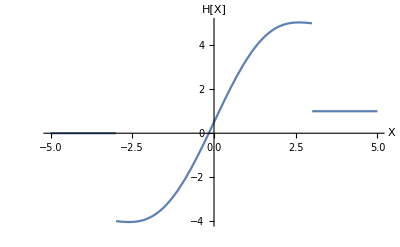

```mathematica
e =3;
H[x_]:=If[x<-e, 0, If[x≥ -e && x≤e,(1/2 + (x/2e) + (1/2Pi)Sin[Pi*x/e]), 1 ]];
Plot[H[x], {x, -5, 5}, AxesLabel-> {"X", "H[X]"}]
```

## Problem 5

Consider the function f(x; y). 

a. Set y = 10^3 and evaluate f(x; y).

```mathematica
myfunction[x_, y_]:= ((x+y)^2-(2x*y)-(y^2))/(x^2);
dataset = Table[{10.0^-i, myfunction[10.0^-i, 10^3], 1-myfunction[10.0^-i, 10^3]}, {i, 8}];
dataheading = PrependTo[dataset, {"x-value", "my function", "Absolute Error"}];
Grid[dataheading, Dividers -> All]
```

x-value | my function | Absolute Error
0.1 | 1. | -9.31322×10^-10
0.01 | 0.999999 | 5.34579×10^-7
0.001 | 1.00001 | -7.61449×10^-6
0.0001 | 1.00117 | -0.00117177
0.00001 | 0. | 1.
1.×10^-6 | 0. | 1.
1.×10^-7 | -11641.5 | 11642.5
1.×10^-8 | 0. | 1.

Repeat part (a) with g(x; y)

```mathematica
myfunction[x_, y_]:=  (((x+y)^2)/(x^2)) - ((2x*y)/(x^2)) -  ((y^2)/(x^2));
dataset = Table[{10.0^-i, myfunction[10.0^-i, 10^3], 1-myfunction[10.0^-i, 10^3]}, {i, 8}];
dataheading = PrependTo[dataset, {"x-value", "my function", "Absolute Error"}];
Grid[dataheading, Dividers -> All]
```

x-value | my function | Absolute Error
0.1 | 1. | 0.
0.01 | 1. | 0.
0.001 | 1. | 0.
0.0001 | 1. | 0.
0.00001 | 0. | 1.
1.×10^-6 | 0. | 1.
1.×10^-7 | -16384. | 16385.
1.×10^-8 | 2.09715×10^6 | -2.09715×10^6

c. Are the two functions identical? Which one are you most likely
to implement to perform calculations in Mathematica involving
small values of x? Give reasons for your answer.

The two functions are identical and if I were to choose the one, I would choose the first function (F(x)) because it has the entire numerator divided by the entire denominator, so when I run the function, there should be less chance of error with mixing up any parenthesis or something. Though according to the data, it seemed that the second function (G(x)) performed better, so possibly the fact that it did not combine everything and ran each part of the function separately actually led to a better answer, since Mathematica does not do well with rounding if the numbers has too many decimals, as they tend to go with convergence which if the number converges to zero, this can lead to a big problem.

d. What role does loss of significance error play in explaining your
results obtained in part (a) and (b)

The role that loss of significance error plays is large in that it rounds to the convergence number if there are too many decimal places, and if the number is supposed to converge to zero, that becomes a huge issue. 

e. Repeat part (a) using.

```mathematica
myfunction[x_, y_]:=  ((x+y)^2-(2x*y)-(y^2))/(x^2);
dataset = Table[{10^-i, myfunction[10^-i, 10^3], 1-myfunction[10^-i, 10^3]}, {i, 8}];
dataheading = PrependTo[dataset, {"x-value", "my function", "Absolute Error"}];
Grid[dataheading, Dividers -> All]
```

x-value | my function | Absolute Error
1/10 | 1 | 0
1/100 | 1 | 0
1/1000 | 1 | 0
1/10000 | 1 | 0
1/100000 | 1 | 0
1/1000000 | 1 | 0
1/10000000 | 1 | 0
1/100000000 | 1 | 0

In this case there is no more error because when we get rid of the decimal for 10.0 and instead use 10, it converts the numbers into fraction instead of decimal. Because of this, there is no more rounding error so we do not have convergence issues which arise for denominators approaching zero.